```mathematica
(*Para ejecutar este programa se tienen que ejecutar los programas: Golden section search y Kramers-Kronig_Dielectric_function y SSKK*)
```

```mathematica
SetDirectory["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\Funciones_dielectricas"]
```

C:\Users\Nanoplasmonics\Documents\GitHub\Tesis-de-Licenciatura\Funciones_dielectricas

## Constantes

```mathematica
h=4.135667696*10^(-15); (*eV s*) (*Constante de Planck*)
ℏ=6.582119569*10^(-16); (*eV s*)(*Constante de Planck reducida*)
c=3*^17 ;(*nm s^-1*)(*Velocidad de la luz*)
omega10=Range[0,10,0.01]; (*Valor de *)
omega30=Range[0,30,0.05];
econst=1.602176634*10^(-19);
```

```mathematica
h c/400
```

3.10175

```mathematica
Clear[epsRe]
```

## Funciones generales

```mathematica
epsRe[parteRe_,parteIm_,x_]:=parteRe[x]^2-parteIm[x]^2;
epsIm[parteRe_,parteIm_,x_]:=(2*parteRe[x]*parteIm[x]);
epsTot[parteRe_,parteIm_,x_]:=epsRe[parteRe,parteIm,x]+I*epsIm[parteRe,parteIm,x];
(*Función para encontrar los máximos alrededor de intervalos dados*)
ω0i[eps_,intervalos_]:=GoldenSearchMax[eps,##]&@@@intervalos;
(*Parte imaginaria de lorentziana*)
lorentzIm[ω_,ω0_,γ_]:=(γ ω)/((ω0^2-ω^2)^2+(γ ω)^2)
(*Definición de 5 lorentzianas*)
lorentzSumIm5[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_]:=A1 lorentzIm[ω,ω01,γ1]+A2 lorentzIm[ω,ω02,γ2]+A3 lorentzIm[ω,ω03,γ3]+ A4 lorentzIm[ω,ω04,γ4]+ A5 lorentzIm[ω,ω05,γ5];
(*Definición de 6 lorentzianas*)
lorentzSumIm6[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_,A6_,ω06_,γ6_]:=A1 lorentzIm[ω,ω01,γ1]+A2 lorentzIm[ω,ω02,γ2]+A3 lorentzIm[ω,ω03,γ3]+ A4 lorentzIm[ω,ω04,γ4]+ A5 lorentzIm[ω,ω05,γ5]+A6 lorentzIm[ω,ω06,γ6];
(*Definición de 4 lorentzianas*)
lorentzSumIm4[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_]:=A1 lorentzIm[ω,ω01,γ1]+A2 lorentzIm[ω,ω02,γ2]+A3 lorentzIm[ω,ω03,γ3]+A4 lorentzIm[ω,ω04,γ4];

(*Parte real de lorentziana*)
lorentzRe[A_,ω_,ω0_,γ_]:=1+(A *(ω0^2-ω^2))/((ω0^2-ω^2)^2+(γ ω)^2)
(*Definición de 6 lorentzianas*)
lorentzSumRe6[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_,A6_,ω06_,γ6_]:= lorentzRe[A1,ω,ω01,γ1]+lorentzRe[A2,ω,ω02,γ2]+ lorentzRe[A3,ω,ω03,γ3]+lorentzRe[A4,ω,ω04,γ4]+lorentzRe[A5,ω,ω05,γ5]+lorentzRe[A6,ω,ω06,γ6];
(*Definición de 4 lorentzianas*)
lorentzSumRe4[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_]:= lorentzRe[A1,ω,ω01,γ1]+lorentzRe[A2,ω,ω02,γ2]+ lorentzRe[A3,ω,ω03,γ3]+lorentzRe[A4,ω,ω04,γ4];
(*Lorentziana compleja*)
lorentz[A_,ω_,ω0_,γ_]:=1+A^2/(ω0^2-ω^2-I*(γ ω))
(*Suma de 6 lorentzianas complejas*)
lorentzSum[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_,A6_,ω06_,γ6_]:=lorentz[A1,ω,ω01,γ1]+lorentz[A2,ω,ω02,γ2]+ lorentz[A3,ω,ω03,γ3]+lorentz[A4,ω,ω04,γ4]+lorentz[A5,ω,ω05,γ5]+lorentz[A6,ω,ω06,γ6];
```

## Concentración 28.7 g/dL

```mathematica
(*Se van a importar los datos de la parte real e imaginaria del índice de refracción*)
datos0Im=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2Im=h c/datos1Im[[All,1]];
(*Se interpolan los datos de la parte imaginaria y real*)
parteIm280=Transpose[{datos2Im,datos1Im[[All,2]]}];
parteIm28=Interpolation[parteIm280,InterpolationOrder->1];
(*Función que da la parte real del índice de refracción a partir de la relación de Meinke 2006*)
datosH2O=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\H2O_n.csv"];
datosBeta=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\Beta_parameter_ReN_Erythrocytes.csv"];
datos1Beta=Drop[datosBeta,1];
datos1H2O=Drop[datosH2O,1];
datos2Beta=h c/datos1Beta[[All,1]];
datos2H2O=h c/(datos1H2O[[All,1]]*1000);
beta=Interpolation[Transpose[{datos2Beta,datos1Beta[[All,2]]}]]
h2o=Interpolation[Transpose[{datos2H2O,datos1H2O[[All,2]]}]];
(*Se va a encontrar la parte real empleando la relación de Meinke 2006*)
parteRe[x_,C_]:=h2o[x]*((beta[x]*C)+1);
parteRe28[x_]:=parteRe[x,28.7];
```

InterpolatingFunction[…]

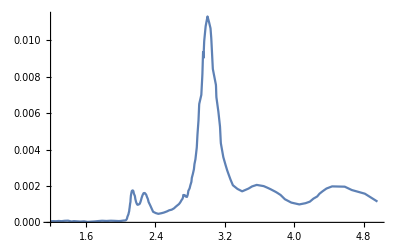

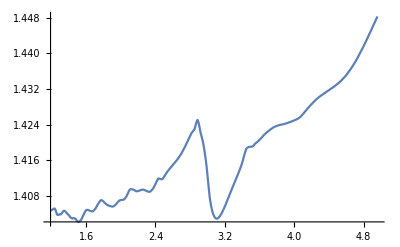

```mathematica
Plot[{parteIm28[x]},{x,1.19,4.96},PlotRange->All]
Plot[{parteRe28[x]},{x,1.19,4.96},PlotRange->All]
```

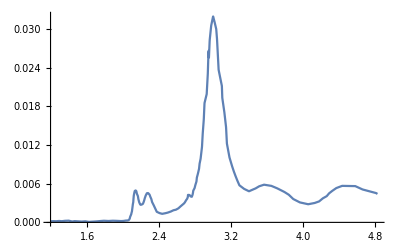

```mathematica
Plot[{epsIm[parteRe28,parteIm28,x]},{x,1.19,4.83},PlotRange->All]
```

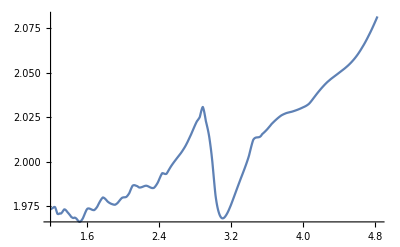

```mathematica
Plot[{epsRe[parteRe28,parteIm28,x]},{x,1.19,4.83},PlotRange->All]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalos28={{2.1,2.2},{2.2,2.4},{2.8,3.3},{3.5,3.8},{4,4.7}};
eps28Im[x_]:=epsIm[parteRe28,parteIm28,x];
eps28Re[x_]:=epsRe[parteRe28,parteIm28,x];
ω0i28=ω0i[eps28Im,intervalos28];
(*Ajuste de la parte imaginaria con lorentzianas*)
{xmin,xmax}={Min[datos2Im],Max[datos2Im]};
```

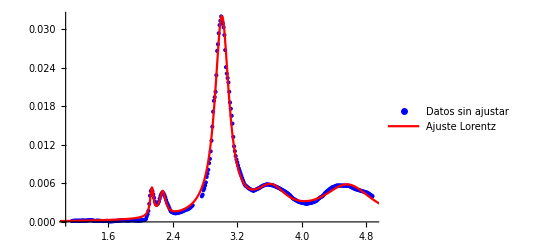

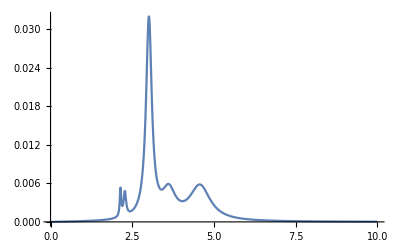

{A1→4.74×10^-4,ω01→2.14,γ1→5.15×10^-2,A2→7.89×10^-4,ω02→2.27,γ2→9.15×10^-2,A3→1.99×10^-2,ω03→3.01,γ3→2.13×10^-1,A4→7.52×10^-3,ω04→3.63,γ4→4.89×10^-1,A5→1.9×10^-2,ω05→4.59,γ5→7.64×10^-1}

{0.000474355,2.13957,0.0515139,0.000789019,2.2735,0.0915299,0.0198978,3.01086,0.212506,0.0075225,3.62506,0.489019,0.0190063,4.58734,0.763838}

```mathematica
(*Datos para ajuste ignorando el pico pequeño faltante*)
eps28Data0=Table[{x,eps28Im[x]},{x,xmin,2.65,0.01}];
eps28Data1=Table[{x,eps28Im[x]},{x,2.76,xmax,0.01}];
eps28Data2=Join[eps28Data0,eps28Data1];
eps28Data=Table[{x,eps28Im[x]},{x,xmin,xmax,0.01}];
(* Ajustar con NonlinearModelFit*)
fit28=NonlinearModelFit[eps28Data2,lorentzSumIm5[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,ω0i28[[1]]},{γ1,0.05},{A2,0.01},{ω02,ω0i28[[2]]},{γ2,0.1},{A3,0.01},{ω03,ω0i28[[3]]},{γ3,0.05},{A4,0.01},{ω04,ω0i28[[4]]},{γ4,0.1},{A5,0.01},{ω05,ω0i28[[5]]},{γ5,0.1}},ω];
(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps28Data2,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit28[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit28[ω],{ω,0,10},PlotRange->All]
ScientificForm[fit28["BestFitParameters"],3]
fit28Values=Values[fit28["BestFitParameters"]]
```

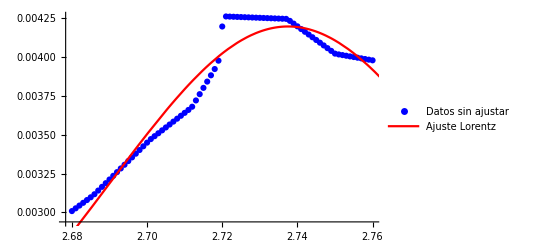

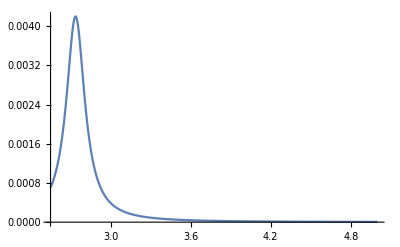

{A1→1.94×10^-3,ω01→2.74,γ1→1.69×10^-1}

{0.00193862,2.73882,0.168666}

```mathematica
(*Datos para ajuste del pico pequeño*)
eps28Data3=Table[{x,eps28Im[x]},{x,2.68,2.76,0.001}];
fit281=NonlinearModelFit[eps28Data3,A1*lorentzIm[ω,ω01,γ1],{{A1,0.0001},{ω01,2.7},{γ1,0.005}},ω];
Show[ListPlot[eps28Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit281[ω],{ω,2.55,3.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit281[ω],{ω,2.55,5},PlotRange->All]
ScientificForm[fit281["BestFitParameters"],3]
fit281Values=Values[fit281["BestFitParameters"]]
```

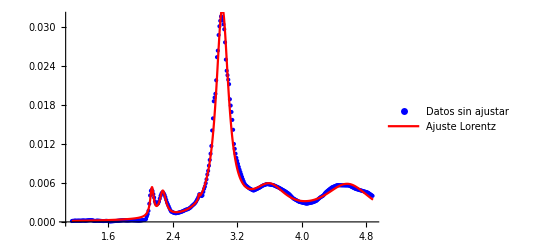

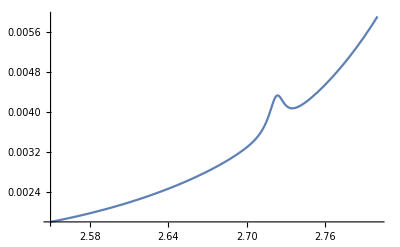

{A1→4.87×10^-4,ω01→2.14,γ1→5.23×10^-2,A2→-8.28×10^-4,ω02→2.27,γ2→-9.33×10^-2,A3→1.8×10^-2,ω03→3.01,γ3→1.87×10^-1,A4→8.47×10^-3,ω04→3.61,γ4→5.23×10^-1,A5→1.84×10^-2,ω05→4.58,γ5→7.37×10^-1,A6→2.66×10^-5,ω06→2.72,γ6→1.44×10^-2}

```mathematica
(*Datos para ajuste total*)
fit28tot=NonlinearModelFit[eps28Data,{lorentzSumIm6[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6],0.002>A6>0&&0.2>γ6>0&&2.77>ω06>2.66},{{A1,fit15Values[[1]]},{ω01,fit15Values[[2]]},{γ1,fit15Values[[3]]},{A2,fit15Values[[4]]},{ω02,fit15Values[[5]]},{γ2,fit15Values[[6]]},{A3,fit15Values[[7]]},{ω03,fit15Values[[8]]},{γ3,fit15Values[[9]]},{A4,fit15Values[[10]]},{ω04,fit15Values[[11]]},{γ4,fit15Values[[12]]},{A5,fit15Values[[13]]},{ω05,fit15Values[[14]]},{γ5,fit15Values[[15]]},{A6,fit151Values[[1]]},{ω06,fit151Values[[2]]},{γ6,fit151Values[[3]]}},ω,Weights->(If[2.6<#<2.8,100,2]&/@(eps28Data[[All,1]]))
];
Show[ListPlot[eps28Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit28tot[ω],{ω,xmin,xmax},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit28tot[ω],{ω,2.55,2.8},PlotRange->All]
ScientificForm[fit28tot["BestFitParameters"],3]
```

```mathematica
fit28tot["BestFitParameters"][1]
```

{A1→0.000487185,ω01→2.13959,γ1→0.0523144,A2→-0.000827823,ω02→2.27432,γ2→-0.0933455,A3→0.0180366,ω03→3.01335,γ3→0.187406,A4→0.00846947,ω04→3.60787,γ4→0.523455,A5→0.0184228,ω05→4.58437,γ5→0.737048,A6→0.0000266127,ω06→2.72288,γ6→0.0143507}[1]

```mathematica
ScientificForm[fit28tot["BestFitParameters"],3]
```

{A1→4.87×10^-4,ω01→2.14,γ1→5.23×10^-2,A2→-8.28×10^-4,ω02→2.27,γ2→-9.33×10^-2,A3→1.8×10^-2,ω03→3.01,γ3→1.87×10^-1,A4→8.47×10^-3,ω04→3.61,γ4→5.23×10^-1,A5→1.84×10^-2,ω05→4.58,γ5→7.37×10^-1,A6→2.66×10^-5,ω06→2.72,γ6→1.44×10^-2}

```mathematica
myA=γ1/. fit28tot["BestFitParameters"]
```

0.0523144

```mathematica
parteIm028=Table[fit28tot[x],{x,1.19,4.96,0.01}];
parteIm02810=Table[fit28tot[x],{x,0,10,0.01}];
omegaprueba28=Range[1.19,4.96,0.01];
datosRealObjetivo28=eps28Re/@omegaprueba28;
funcionError28[w_?NumericQ]:=Module[{epsAnchor,espectro,dif},(*valor de epsReal en el ancla*)
epsAnchor=eps28Re[w];
(*ejecutar modelo*)espectro=sskkrebook[omegaprueba28,parteIm028,w,epsAnchor];
(*error cuadrático total*)dif=espectro-datosRealObjetivo28;
Sqrt[Total[dif^2]/Length[datosRealObjetivo28]]];
```

InterpolatingFunction::dmval: Input value {4.89} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.91} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
h c/400
h c/600
```

3.10175

2.06783

```mathematica
parteReSSKK28=Table[{w,funcionError28[w]},{w,2.05,3.1,0.01}];
```

Set::setraw: Cannot assign to raw object {1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,«368»}.

Set::setraw: Cannot assign to raw object 0.000159043.

Set::setraw: Cannot assign to raw object 0.000161204.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
MinimalBy[parteReSSKK28,Last]
```

{{2.85,0.0368551}}

```mathematica
parteReSSKK28=sskkrebook[omega10,parteIm02810,2.85,eps28Re[2.85]];
partere282=Interpolation[Transpose[{omega10,parteReSSKK28}]];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.02016×10^-6.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
parteim282=Interpolation[Transpose[{omega10,parteIm02810}]]
```

InterpolatingFunction[…]

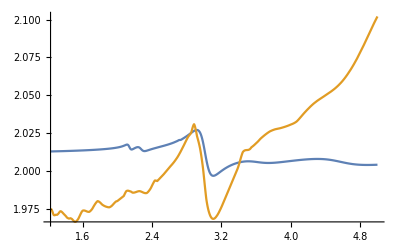

```mathematica
Plot[{partere282[x],epsRe[parteRe28,parteIm28,x]},{x,1.23,5},PlotRange->All]
```

```mathematica
epsEritrocitosData28=Table[{w*0.2418,partere282[w],parteim282[w]},{w,1,10,0.01}];
Export["epsEritrocitosData28.csv",epsEritrocitosData28]
```

epsEritrocitosData28.csv

## Concentración 15.3 g/dL

```mathematica
(*Se van a importar los datos de la parte real del índice de refracción y del coeficiente de absorción*)
datosuA=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\15.3_uA_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1uA=Drop[datosuA,1];
datos1uA=Map[ToExpression,datos1uA,{2}];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2im=h c/datos1uA[[All,1]];
(*Obtener la parte imaginaria del índice de refracción a partir del coeficiente de absorción*)
datos3im=((datos1uA[[All,2]]*10^(-6))/(4*Pi))*datos1uA[[All,1]];
(*Se interpolan los datos de la parte imaginaria*)
parteIm15=Interpolation[Transpose[{datos2im,datos3im}],InterpolationOrder->1];
parteRe15[x_]:=parteRe[x,15.3]
```

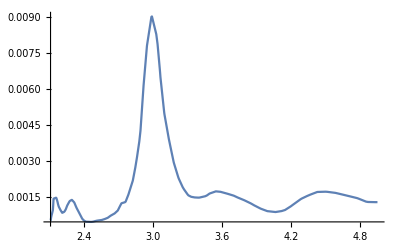

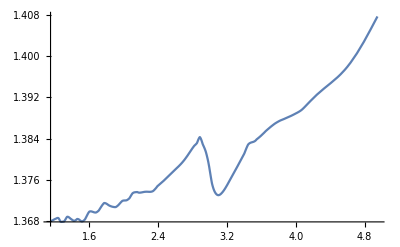

```mathematica
Plot[parteIm15[x],{x,2.11,4.95},PlotRange->All]
Plot[parteRe15[x],{x,1.15,4.95},PlotRange->All]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalos15={{2.13,2.15},{2.2,2.3},{2.8,3.2},{3.4,3.7},{4.2,4.7}};
eps15Im[x_]:=epsIm[parteRe15,parteIm15,x];
eps15Re[x_]:=epsRe[parteRe15,parteIm15,x];
ω0i15=ω0i[eps15Im,intervalos15];
```

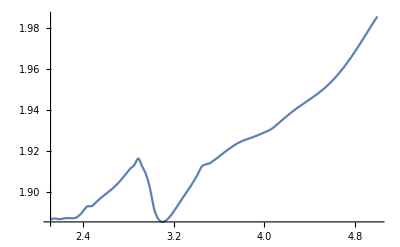

```mathematica
Plot[eps15Re[x],{x,2.11,5}]
```

{A1→3.84×10^-4,ω01→2.16,γ1→5.39×10^-2,A2→7.×10^-4,ω02→2.29,γ2→1.01×10^-1,A3→1.52×10^-2,ω03→3.,γ3→2.09×10^-1,A4→6.06×10^-3,ω04→3.6,γ4→5.09×10^-1,A5→1.82×10^-2,ω05→4.61,γ5→8.74×10^-1}

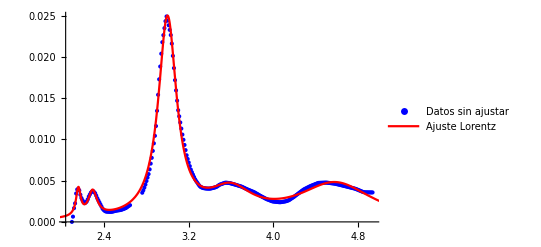

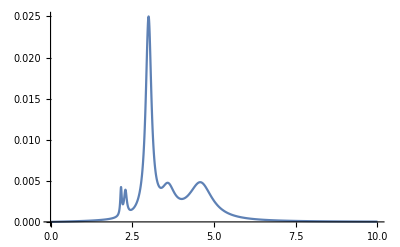

{0.000383677,2.15572,0.0539125,0.000699595,2.29116,0.1008,0.0151683,3.00063,0.209204,0.00605578,3.603,0.509093,0.0182062,4.60912,0.874277}

```mathematica
(*Ajuste de la parte imaginaria con lorentzianas*)
{xmin15,xmax15}={Min[datos2im],Max[datos2im]};
(*Datos para ajuste*)
(*Datos para ajuste ignorando el pico pequeño faltante*)
eps15Data0=Table[{x,eps15Im[x]},{x,xmin15,2.65,0.01}];
eps15Data1=Table[{x,eps15Im[x]},{x,2.76,xmax15,0.01}];
eps15Data2=Join[eps15Data0,eps15Data1];
eps15Data=Table[{x,eps15Im[x]},{x,xmin15,xmax15,0.01}];

(* Ajustar ignorando el pico pequeño*)
fit15=NonlinearModelFit[eps15Data2,lorentzSumIm5[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,ω0i15[[1]]},{γ1,0.05},{A2,0.01},{ω02,ω0i15[[2]]},{γ2,0.1},{A3,0.01},{ω03,ω0i15[[3]]},{γ3,0.1},{A4,0.01},{ω04,ω0i15[[4]]},{γ4,0.1},{A5,0.01},{ω05,ω0i15[[5]]},{γ5,0.1}},ω];
ScientificForm[fit15["BestFitParameters"],3]
(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps15Data2,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit15[ω],{ω,xmin15-0.5,xmax15+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit15[ω],{ω,0,10},PlotRange->All]
fit15Values=Values[fit15["BestFitParameters"]]
```

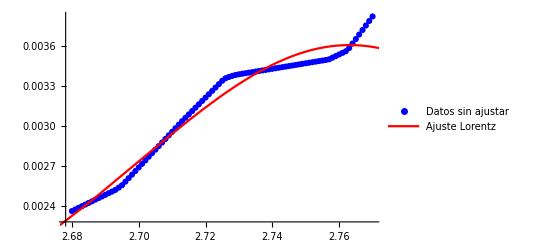

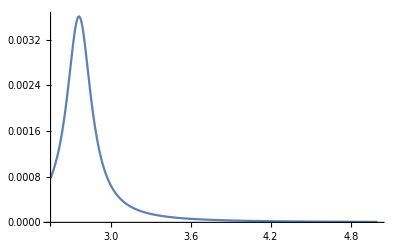

{A1→2.23×10^-3,ω01→2.77,γ1→2.23×10^-1}

{0.00222613,2.76539,0.22337}

```mathematica
(*Datos para ajuste del pico pequeño*)
eps15Data3=Table[{x,eps15Im[x]},{x,2.68,2.77,0.001}];
fit151=NonlinearModelFit[eps15Data3,A1*lorentzIm[ω,ω01,γ1],{{A1,0.0001},{ω01,2.75},{γ1,0.005}},ω];
Show[ListPlot[eps15Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit151[ω],{ω,2.55,3.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit151[ω],{ω,2.55,5},PlotRange->All]
ScientificForm[fit151["BestFitParameters"],3]
fit151Values=Values[fit151["BestFitParameters"]]
```

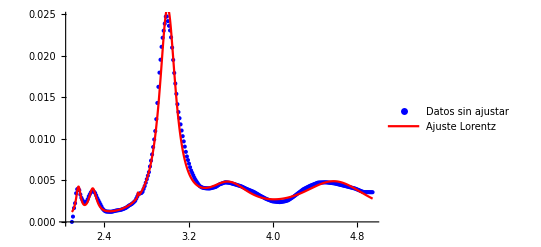

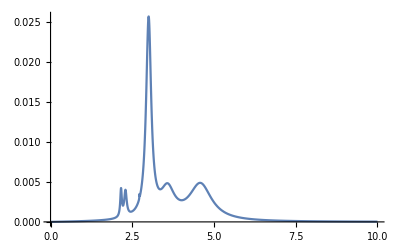

{A1→4.13×10^-4,ω01→2.16,γ1→5.61×10^-2,A2→6.64×10^-4,ω02→2.29,γ2→9.01×10^-2,A3→1.39×10^-2,ω03→3.,γ3→1.86×10^-1,A4→6.55×10^-3,ω04→3.59,γ4→5.14×10^-1,A5→1.76×10^-2,ω05→4.6,γ5→8.32×10^-1,A6→1.15×10^-5,ω06→2.72,γ6→7.83×10^-3}

```mathematica
(*Datos para ajuste total*)
fit15tot=NonlinearModelFit[eps15Data,{lorentzSumIm6[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6],0.002>A6>0&&0.2>γ6>0&&2.77>ω06>2.66},{{A1,fit15Values[[1]]},{ω01,fit15Values[[2]]},{γ1,fit15Values[[3]]},{A2,fit15Values[[4]]},{ω02,fit15Values[[5]]},{γ2,fit15Values[[6]]},{A3,fit15Values[[7]]},{ω03,fit15Values[[8]]},{γ3,fit15Values[[9]]},{A4,fit15Values[[10]]},{ω04,fit15Values[[11]]},{γ4,fit15Values[[12]]},{A5,fit15Values[[13]]},{ω05,fit15Values[[14]]},{γ5,fit15Values[[15]]},{A6,fit151Values[[1]]},{ω06,fit151Values[[2]]},{γ6,fit151Values[[3]]}},ω,Weights->(If[2.6<#<2.8,100,2]&/@(eps15Data[[All,1]]))
];
Show[ListPlot[eps15Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit15tot[ω],{ω,xmin15,xmax15},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit15tot[ω],{ω,0,10},PlotRange->All]
ScientificForm[fit15tot["BestFitParameters"],3]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 8.79827×10^-7.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

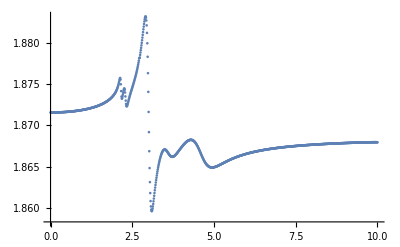

```mathematica
(*Obtención de la parte real a partir de la parte imaginaria con KK*)
parteIm015=Table[fit15tot[x],{x,0,10,0.01}];
parteReSSKK15=sskkrebook[omega10,parteIm015,1.15,1.872];
ListPlot[Transpose[{omega10,parteReSSKK15}],PlotRange->All]
```

```mathematica
xmin15
xmax15
```

2.09433

4.9448

```mathematica
omegaprueba=Range[2.11,4.94,0.01];
data=Table[fit15tot[x],{x,2.11,4.94,0.01}];
dataexp=eps15Re/@omegaprueba;
```

```mathematica
Length[data]
Length[dataexp]
```

284

284

```mathematica
parteIm015=Table[fit15tot[x],{x,2.11,4.94,0.01}];
parteIm01510=Table[fit15tot[x],{x,0,10,0.01}];
```

```mathematica
datosRealObjetivo15=eps15Re/@omegaprueba;
funcionError15[w_?NumericQ]:=Module[{epsAnchor,espectro,dif},(*valor de epsReal en el ancla*)
epsAnchor=eps15Re[w];
(*ejecutar modelo*)espectro=sskkrebook[omegaprueba,parteIm015,w,epsAnchor];
(*error cuadrático total*)dif=espectro-datosRealObjetivo15;
Sqrt[Total[dif^2]/Length[datosRealObjetivo15]]]
```

```mathematica
hola15=Table[{w,funcionError15[w]},{w,2.11,4.94,0.01}];
```

Set::setraw: Cannot assign to raw object {2.11,2.12,2.13,2.14,2.15,2.16,2.17,2.18,2.19,2.2,«274»}.

Set::setraw: Cannot assign to raw object 0.00157173.

Set::setraw: Cannot assign to raw object 0.00196142.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
MinimalBy[hola15,Last]
```

{{3.59,0.0284904}}

```mathematica
parteReSSKK15=sskkrebook[omega10,parteIm01510,3.59,eps15Re[3.59]];
partere152=Interpolation[Transpose[{omega10,parteReSSKK15}]];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 8.79827×10^-7.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.30008} lies outside the range of data in the interpolating function. Extrapolation will be used.

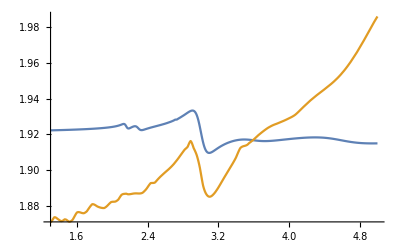

```mathematica
Plot[{partere152[x],eps15Re[x]},{x,1.3,5},PlotRange->All]
```

## Concentración 30.6 g/dL

```mathematica
(*Se van a importar los datos de la parte real del índice de refracción y del coeficiente de absorción*)
```

```mathematica
datosuA30=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\30.6_uA_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1uA30=Drop[datosuA30,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2im30=h c/datos1uA30[[All,1]];
(*Obtener la parte imaginariad del índice de refracción a partir del coeficiente de absorción*)
datos3im30=datos1uA30[[All,2]]*10^(-6)*datos1uA30[[All,1]]/(4*Pi);
(*Se interpolan los datos de la parte imaginaria*)
parteIm30=Interpolation[Transpose[{datos2im30,datos3im30}],InterpolationOrder->1];
parteRe30[x_]:=parteRe[x,30.6]
```

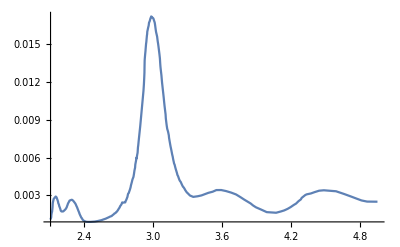

```mathematica
Plot[parteIm30[x],{x,2.11,4.95},PlotRange->All]
```

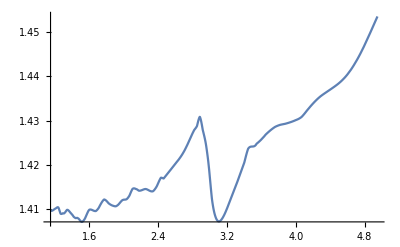

```mathematica
Plot[parteRe30[x],{x,1.15,4.95}]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalos30={{2.07,2.1},{2.15,2.4},{2.8,3.2},{3.4,3.7},{4.2,4.7}};
eps30Im[x_]:=epsIm[parteRe30,parteIm30,x];
eps30Re[x_]:=epsRe[parteRe30,parteIm30,x];
ω0i30=ω0i[eps30Im,intervalos30];
```

```mathematica
ω0i30
```

{2.1,2.29299,2.98423,3.59246,4.48442}

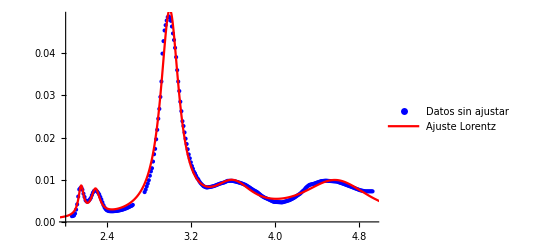

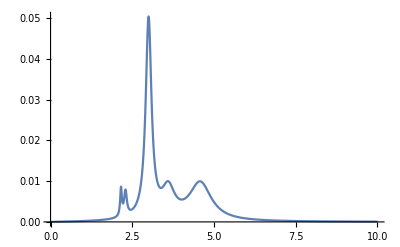

{0.000893659,2.15559,0.0611478,0.00140038,2.29281,0.100361,0.031168,3.0009,0.212855,0.0121534,3.60747,0.473292,0.0351298,4.59777,0.819342}

{A1→8.94×10^-4,ω01→2.16,γ1→6.11×10^-2,A2→1.4×10^-3,ω02→2.29,γ2→1.×10^-1,A3→3.12×10^-2,ω03→3.,γ3→2.13×10^-1,A4→1.22×10^-2,ω04→3.61,γ4→4.73×10^-1,A5→3.51×10^-2,ω05→4.6,γ5→8.19×10^-1}

```mathematica
(* Ajustar ignorando el pico pequeño*)
{xmin30,xmax30}={Min[datos2im30],Max[datos2im30]};
eps30Data0=Table[{x,eps30Im[x]},{x,xmin30,2.65,0.01}];
eps30Data1=Table[{x,eps30Im[x]},{x,2.76,xmax30,0.01}];
eps30Data2=Join[eps30Data0,eps30Data1];
eps30Data=Table[{x,eps30Im[x]},{x,xmin30,xmax30,0.01}];

(* Ajustar con NonlinearModelFit*)
fit30=NonlinearModelFit[eps30Data2,lorentzSumIm5[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,ω0i30[[1]]},{γ1,0.01},{A2,0.01},{ω02,ω0i30[[2]]},{γ2,0.05},{A3,0.01},{ω03,ω0i30[[3]]},{γ3,0.1},{A4,0.01},{ω04,ω0i30[[4]]},{γ4,0.1},{A5,0.01},{ω05,ω0i30[[5]]},{γ5,0.1}},ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps30Data2,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit30[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit30[ω],{ω,0,10},PlotRange->All]
fit30Values=Values[fit30["BestFitParameters"]]
ScientificForm[fit30["BestFitParameters"],3]
```

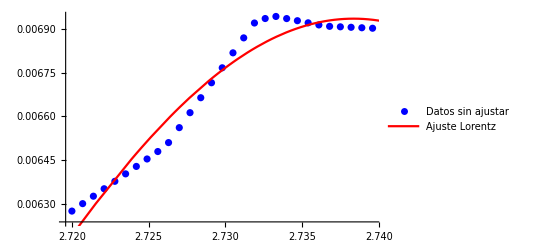

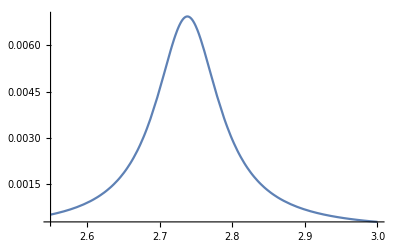

{A1→2.02×10^-3,ω01→2.74,γ1→1.06×10^-1}

{0.00201572,2.73888,0.106147}

```mathematica
(*Datos para ajuste del pico pequeño*)
eps30Data3=Table[{x,eps30Im[x]},{x,2.72,2.74,0.0007}];
fit301=NonlinearModelFit[eps30Data3,A1*lorentzIm[ω,ω01,γ1],{{A1,0.0001},{ω01,2.75},{γ1,0.005}},ω];
Show[ListPlot[eps30Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit301[ω],{ω,2.55,3.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit301[ω],{ω,2.55,3},PlotRange->All]
ScientificForm[fit301["BestFitParameters"],3]
fit301Values=Values[fit301["BestFitParameters"]]
```

```mathematica
fit30Values[[3]]
```

0.0611478

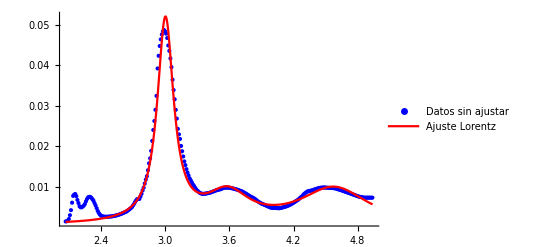

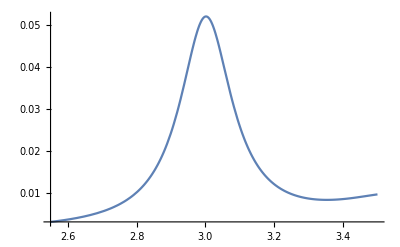

{A1→2.27×10^4,ω01→1.×10^5,γ1→1.×10^5,A2→8.48×10^1,ω02→-5.91×10^-1,γ2→2.×10^5,A3→2.78×10^-2,ω03→3.,γ3→1.85×10^-1,A4→1.31×10^-2,ω04→3.59,γ4→4.94×10^-1,A5→3.37×10^-2,ω05→4.6,γ5→7.96×10^-1,A6→8.48×10^1,ω06→2.72,γ6→2.×10^5}

```mathematica
fit30tot=NonlinearModelFit[eps30Data,{lorentzSumIm6[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6],A2>0&&A1>0&&A5>0&&A6>0&&γ6>0&&2.77>ω06>2.66&&γ1>0&&γ2>0&&ω01>0},{{A1,fit30Values[[1]]},{ω01,fit30Values[[2]]},{γ1,fit30Values[[3]]},{A2,fit30Values[[4]]},{ω02,fit30Values[[5]]},{γ2,fit30Values[[6]]},{A3,fit30Values[[7]]},{ω03,fit30Values[[8]]},{γ3,fit30Values[[9]]},{A4,fit30Values[[10]]},{ω04,fit30Values[[11]]},{γ4,fit30Values[[12]]},{A5,fit30Values[[13]]},{ω05,fit30Values[[14]]},{γ5,fit30Values[[15]]},{A6,fit301Values[[1]]},{ω06,fit301Values[[2]]},{γ6,fit30Values[[3]]}},ω,Weights->(If[2.6<#<2.8,100,2]&/@(eps30Data[[All,1]]))
];
Show[ListPlot[eps30Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit30tot[ω],{ω,xmin30,xmax30},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All],PlotRange->All]
Plot[fit30tot[ω],{ω,2.55,3.5},PlotRange->All]
ScientificForm[fit30tot["BestFitParameters"],3]
```

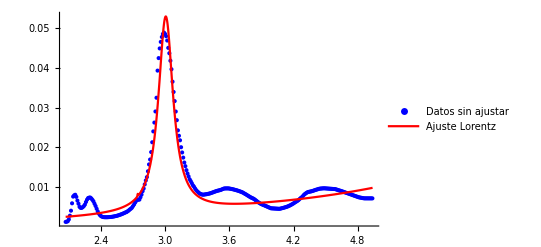

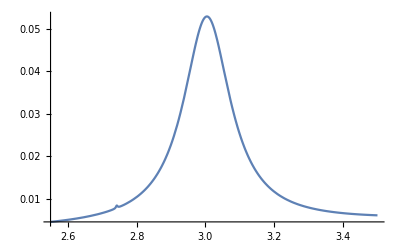

{A1→9.19×10^-4,ω01→3.09×10^-4,γ1→3.33×10^2,A2→1.04×10^-3,ω02→-4.8×10^-1,γ2→3.79×10^2,A3→2.46×10^-2,ω03→3.01,γ3→1.67×10^-1,A4→2.09×10^1,ω04→9.04,γ4→3.13×10^-1,A5→1.39×10^2,ω05→3.42×10^2,γ5→1.92×10^2,A6→1.×10^-5,ω06→2.74,γ6→6.04×10^-3}

```mathematica
(*Datos para ajuste total*)
fit30tot=NonlinearModelFit[eps30Data,{lorentzSumIm6[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6],A4>0&&A1>0&&A2>0&&A3>0&&A5>0&&γ1>0&&γ2>0&&γ3>0&&γ4>0&&γ5>0&&0.0001>A6>0.00001&&0.008>γ6>0.006&&2.76>ω06>2.72},{{A1,fit15Values[[1]]},{ω01,fit15Values[[2]]},{γ1,fit15Values[[3]]},{A2,fit15Values[[4]]},{ω02,fit15Values[[5]]},{γ2,fit15Values[[6]]},{A3,fit15Values[[7]]},{ω03,fit15Values[[8]]},{γ3,fit15Values[[9]]},{A4,fit15Values[[10]]},{ω04,fit15Values[[11]]},{γ4,fit15Values[[12]]},{A5,fit15Values[[13]]},{ω05,fit15Values[[14]]},{γ5,fit15Values[[15]]},{A6,fit151Values[[1]]},{ω06,fit151Values[[2]]},{γ6,fit151Values[[3]]}},ω,Weights->(If[2.72<#<2.8,70,2]&/@(eps30Data[[All,1]]))
];
Show[ListPlot[eps30Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit30tot[ω],{ω,xmin30,xmax30},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All],PlotRange->All]
Plot[fit30tot[ω],{ω,2.55,3.5},PlotRange->All]
ScientificForm[fit30tot["BestFitParameters"],3]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.88751×10^-6.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

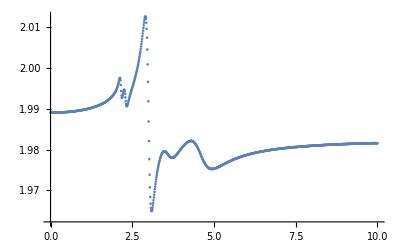

```mathematica
(*Obtención de la parte real a partir de la parte imaginaria con KK*)
parteIm030=Table[fit30tot[x],{x,0,10,0.01}];
parteReSSKK30=sskkrebook[omega10,parteIm030,1.15,1.99];
ListPlot[Transpose[{omega10,parteReSSKK30}],PlotRange->All]
```

```mathematica
parteIm030=Table[fit30[x],{x,2.11,4.95,0.01}];
parteIm03010=Table[fit30[x],{x,0,10,0.01}];
omegaprueba30=Range[2.11,4.95,0.01];
datosRealObjetivo30=eps30Re/@omegaprueba30;
funcionError30[w_?NumericQ]:=Module[{epsAnchor,espectro,dif},(*valor de epsReal en el ancla*)
epsAnchor=eps30Re[w];
(*ejecutar modelo*)espectro=sskkrebook[omegaprueba30,parteIm030,w,epsAnchor];
(*error cuadrático total*)dif=espectro-datosRealObjetivo30;
Sqrt[Total[dif^2]/Length[datosRealObjetivo30]]];
```

InterpolatingFunction::dmval: Input value {4.94} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.95} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
h c/400
h c/600
```

3.10175

2.06783

```mathematica
parteReSSKK30=Table[{w,funcionError30[w]},{w,2.11,3.1,0.01}];
```

Set::setraw: Cannot assign to raw object {2.11,2.12,2.13,2.14,2.15,2.16,2.17,2.18,2.19,2.2,«275»}.

Set::setraw: Cannot assign to raw object 0.00359266.

Set::setraw: Cannot assign to raw object 0.00444197.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
MinimalBy[parteReSSKK30,Last]
```

{{2.88,0.0398841}}

```mathematica
Clear[partere302]
```

```mathematica
parteReSSKK30=sskkrebook[omega10,parteIm03010,2.88,eps30Re[2.88]];
partere302=Interpolation[Transpose[{omega10,parteReSSKK30}]];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.878×10^-6.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
parteim302=Interpolation[Transpose[{omega10,parteIm03010}]]
```

InterpolatingFunction[…]

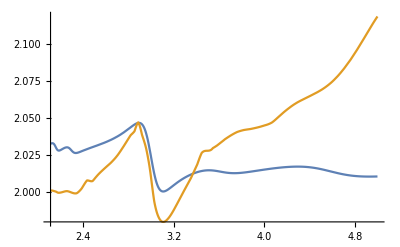

```mathematica
Plot[{partere302[x],eps30Re[x]},{x,2.11,5},PlotRange->All]
```

```mathematica
h c/5
```

248.14

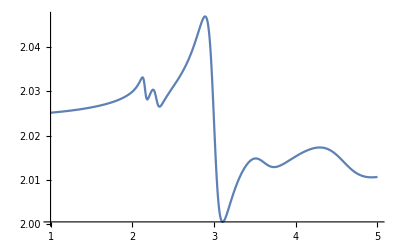

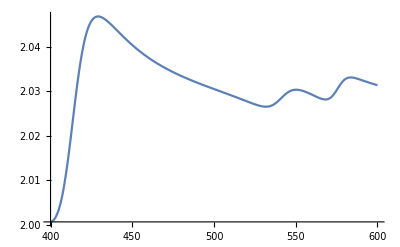

```mathematica
Plot[{partere302[x]},{x,1,5},PlotRange->All]
Plot[{partere302[h c/x]},{x,400,600},PlotRange->All]
```

```mathematica
h c/1000
```

1.2407

```mathematica
partere302[h c/650]
parteim302[h c/650]
```

2.03018

0.000935569

```mathematica
3.10175*0.2418
1.2407003088*0.2418
```

0.750003

0.300001

```mathematica
partere302[h c/500]
```

2.02596

```mathematica
parteim302=Interpolation[Transpose[{omega10,parteIm03010}]]
```

InterpolatingFunction[…]

```mathematica
epsEritrocitosData30=Table[{w*0.2418,partere302[w],parteim302[w]},{w,1,10,0.01}];
Export["epsEritrocitosData30.csv",epsEritrocitosData30]
```

epsEritrocitosData30.csv

```mathematica
epsEritrocitosData30=Table[{(h c/l)*0.2418,partere302[h c/l],parteim302[h c/l]},{l,350,850,50}];
Export["epsEritrocitosData30.csv",epsEritrocitosData30]
```

epsEritrocitosData30.csv

```mathematica
epsEritrocitosData30
```

{{0.857147,2.01616,0.0100466},{0.750003,2.00192,0.0248026},{0.66667,2.04141,0.00796953},{0.600003,2.03158,0.00281195},{0.545457,2.0316,0.00619635},{0.500002,2.03288,0.00206064},{0.461541,2.03018,0.000935569},{0.428573,2.0291,0.000689786},{0.400002,2.02845,0.000562206},{0.375002,2.02801,0.000479731},{0.352943,2.02769,0.000420824}}

```mathematica
0.2418*h c/1000
```

0.300001

```mathematica
partere302[1]
```

2.02664

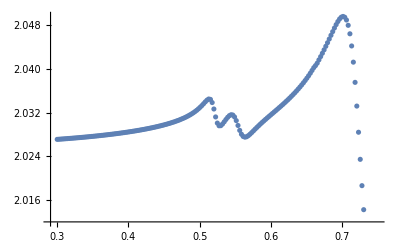

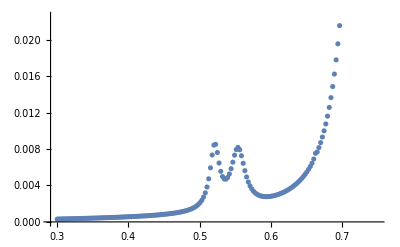

```mathematica
ListPlot[Table[{w*0.2418,partere302[w]},{w,1.2407003088,h c/400,0.01}]]
ListPlot[Table[{w*0.2418,parteim302[w]},{w,1.2407003088,h c/400,0.01}]]
```

## 34 g/dL

```mathematica
parteRe34[x_]:=parteRe[x,34];
parteIm34[x_]:=(34/30)*parteIm30[x];
```

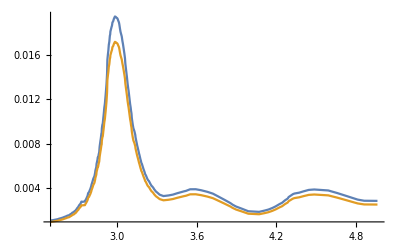

```mathematica
Plot[{parteIm34[x],parteIm30[x]},{x,2.5,4.96},PlotRange->All]
```

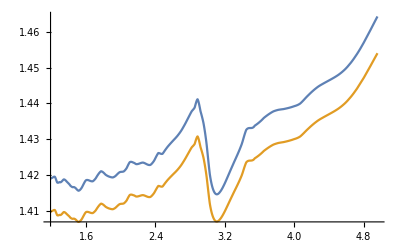

```mathematica
Plot[{parteRe34[x],parteRe30[x]},{x,1.19,4.96}]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalos34={{2.07,2.1},{2.15,2.4},{2.8,3.2},{3.4,3.7},{4.2,4.7}};
eps34Im[x_]:=epsIm[parteRe34,parteIm34,x];
eps34Re[x_]:=epsRe[parteRe34,parteIm34,x];
ω0i34=ω0i[eps34Im,intervalos34];
```

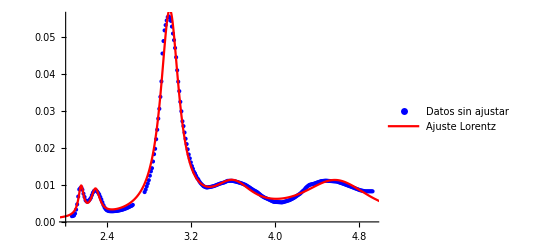

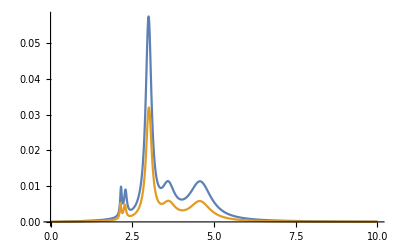

{A1→1.02×10^-3,ω01→2.16,γ1→6.11×10^-2,A2→1.6×10^-3,ω02→2.29,γ2→1.×10^-1,A3→3.55×10^-2,ω03→3.,γ3→2.13×10^-1,A4→1.39×10^-2,ω04→3.61,γ4→4.73×10^-1,A5→4.01×10^-2,ω05→4.6,γ5→8.2×10^-1}

{0.00101927,2.15559,0.0611464,0.00159724,2.2928,0.100367,0.0355376,3.0008,0.212817,0.0138633,3.60746,0.473294,0.0400862,4.59786,0.819547}

```mathematica
(*Datos para ajuste ignorando el pico pequeño faltante*)
eps34Data0=Table[{x,eps34Im[x]},{x,xmin30,2.65,0.01}];
eps34Data1=Table[{x,eps34Im[x]},{x,2.76,xmax30,0.01}];
eps34Data2=Join[eps34Data0,eps34Data1];
eps34Data=Table[{x,eps34Im[x]},{x,xmin30,xmax30,0.01}];
(* Ajustar con NonlinearModelFit*)
fit34=NonlinearModelFit[eps34Data2,lorentzSumIm5[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,ω0i28[[1]]},{γ1,0.05},{A2,0.01},{ω02,ω0i28[[2]]},{γ2,0.1},{A3,0.01},{ω03,ω0i28[[3]]},{γ3,0.05},{A4,0.01},{ω04,ω0i28[[4]]},{γ4,0.1},{A5,0.01},{ω05,ω0i28[[5]]},{γ5,0.1}},ω];
(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps34Data2,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit34[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[{fit34[ω],fit28[ω]},{ω,0,10},PlotRange->All]
ScientificForm[fit34["BestFitParameters"],3]
fit34Values=Values[fit34["BestFitParameters"]]
```

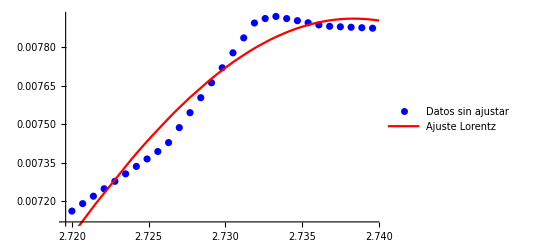

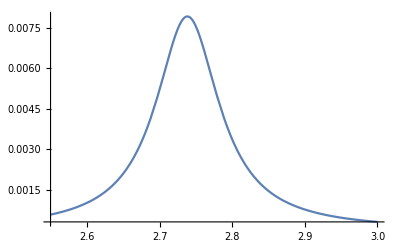

{A1→2.3×10^-3,ω01→2.74,γ1→1.06×10^-1}

{0.00230001,2.73888,0.106143}

```mathematica
(*Datos para ajuste del pico pequeño*)
eps34Data3=Table[{x,eps34Im[x]},{x,2.72,2.74,0.0007}];
fit341=NonlinearModelFit[eps34Data3,A1*lorentzIm[ω,ω01,γ1],{{A1,0.0001},{ω01,2.75},{γ1,0.005}},ω];
Show[ListPlot[eps34Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit341[ω],{ω,2.55,3.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit341[ω],{ω,2.55,3},PlotRange->All]
ScientificForm[fit341["BestFitParameters"],3]
fit301Values=Values[fit341["BestFitParameters"]]
```

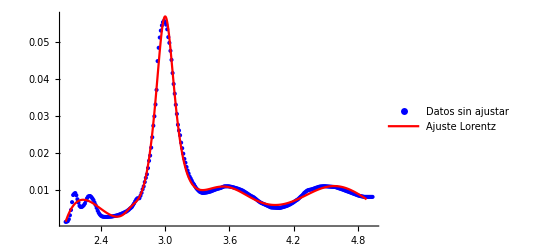

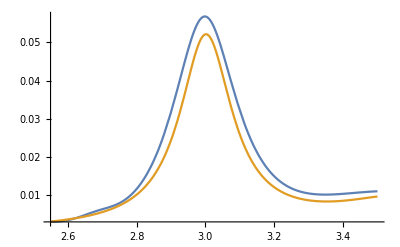

{A1→2.27×10^4,ω01→1.×10^5,γ1→1.×10^5,A2→8.48×10^1,ω02→-5.91×10^-1,γ2→2.×10^5,A3→2.78×10^-2,ω03→3.,γ3→1.85×10^-1,A4→1.31×10^-2,ω04→3.59,γ4→4.94×10^-1,A5→3.37×10^-2,ω05→4.6,γ5→7.96×10^-1,A6→8.48×10^1,ω06→2.72,γ6→2.×10^5}

```mathematica
(*Datos para ajuste total*)
fit34tot=NonlinearModelFit[eps34Data,{lorentzSumIm6[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6],0.002>A6>0&&0.2>γ6>0&&2.77>ω06>2.66},{{A1,fit28Values[[1]]},{ω01,fit28Values[[2]]},{γ1,fit28Values[[3]]},{A2,fit28Values[[4]]},{ω02,fit28Values[[5]]},{γ2,fit28Values[[6]]},{A3,fit28Values[[7]]},{ω03,fit28Values[[8]]},{γ3,fit28Values[[9]]},{A4,fit34Values[[10]]},{ω04,fit34Values[[11]]},{γ4,fit34Values[[12]]},{A5,fit34Values[[13]]},{ω05,fit34Values[[14]]},{γ5,fit34Values[[15]]},{A6,fit151Values[[1]]},{ω06,fit151Values[[2]]},{γ6,fit151Values[[3]]}},ω,Weights->(If[2.6<#<2.8,100,2]&/@(eps34Data[[All,1]]))
];

Show[ListPlot[eps34Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit34tot[ω],{ω,xmin30,xmax},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All],PlotRange->All]
Plot[{fit34tot[ω],fit30tot[ω]},{ω,2.55,3.5},PlotRange->All]
ScientificForm[fit30tot["BestFitParameters"],3]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 2.03421×10^-6.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

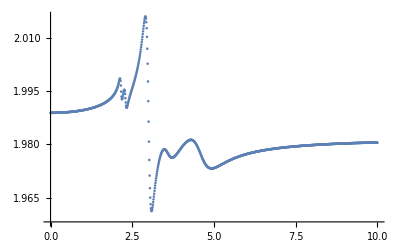

```mathematica
(*Obtención de la parte real a partir de la parte imaginaria con KK*)
parteIm034=Table[fit34tot[x],{x,0,10,0.01}];
parteReSSKK34=sskkrebook[omega10,parteIm034,1.15,1.99];
ListPlot[Transpose[{omega10,parteReSSKK34}],PlotRange->All]
```

```mathematica
parteIm034=Table[fit34[x],{x,1.15,4.95,0.01}];
parteIm03410=Table[fit34[x],{x,0,10,0.01}];
omegaprueba34=Range[1.15,4.95,0.01];
datosRealObjetivo34=eps34Re/@omegaprueba34;
funcionError34[w_?NumericQ]:=Module[{epsAnchor,espectro,dif},(*valor de epsReal en el ancla*)
epsAnchor=eps34Re[w];
(*ejecutar modelo*)espectro=sskkrebook[omegaprueba34,parteIm034,w,epsAnchor];
(*error cuadrático total*)dif=espectro-datosRealObjetivo34;
Sqrt[Total[dif^2]/Length[datosRealObjetivo34]]];
```

InterpolatingFunction::dmval: Input value {1.15} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.16} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.17} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
parteReSSKK34=Table[{w,funcionError34[w]},{w,2.11,3.1,0.01}];
```

Set::setraw: Cannot assign to raw object {1.15,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,«371»}.

Set::setraw: Cannot assign to raw object 0.000316668.

Set::setraw: Cannot assign to raw object 0.000320988.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
MinimalBy[parteReSSKK34,Last]
```

{{2.88,0.0414541}}

```mathematica
Clear[partere302]
```

```mathematica
parteReSSKK34=sskkrebook[omega10,parteIm03410,2.88,eps34Re[2.88]];
partere342=Interpolation[Transpose[{omega10,parteReSSKK34}]];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 2.14216×10^-6.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
Clear[parteIm342]
```

```mathematica
parteim342=Interpolation[Transpose[{omega10,parteIm03410}]]
```

InterpolatingFunction[…]

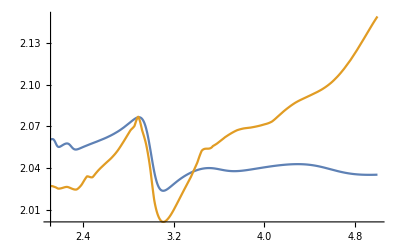

```mathematica
Plot[{partere342[x],eps34Re[x]},{x,2.11,5},PlotRange->All]
```

```mathematica
h c/5
```

248.14

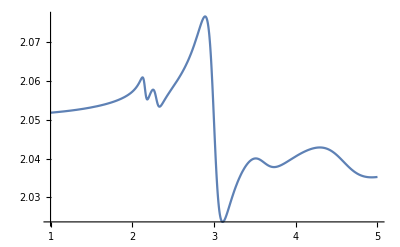

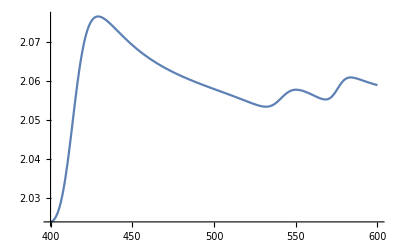

```mathematica
Plot[{partere342[x]},{x,1,5},PlotRange->All]
Plot[{partere342[h c/x]},{x,400,600},PlotRange->All]
```

```mathematica
epsEritrocitosData34=Table[{w*0.2418,partere342[w],parteim342[w]},{w,1,10,0.01}];
Export["epsEritrocitosData34.csv",epsEritrocitosData34]
```

epsEritrocitosData34.csv

## Comparación entre concentraciones

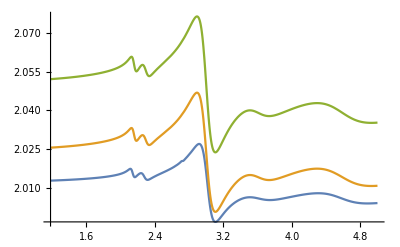

```mathematica
Plot[{partere282[x],partere302[x],partere342[x]},{x,1.18,5},PlotRange->All]
```

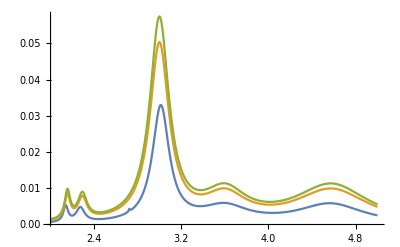

```mathematica
Plot[{fit28tot[x],fit30[x],fit34[x]},{x,2,5},PlotRange->All]
```

## Plasma

```mathematica
(*Se van a importar los datos de la parte real del índice de refracción y del coeficiente de absorción*)
datosuAPlasma=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\uA_ImN_Plasma.csv"];
datosRePlasma=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\ReN_Plasma.csv"];
(*Se eliminan los encabezados de los datos*)
datos1uAPlasma=Drop[datosuAPlasma,1];
datos1RePlasma=Drop[datosRePlasma,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2imPlasma=h c/datos1uAPlasma[[All,1]];
datos2rePlasma=h c/datos1RePlasma[[All,1]];
(*Obtener la parte imaginariad del índice de refracción a partir del coeficiente de absorción*)
datos3imPlasma=datos1uAPlasma[[All,2]]*10^(-6)*datos1uAPlasma[[All,1]]/(4*Pi);
(*Se interpolan los datos de la parte imaginaria*)
parteImPlasma=Interpolation[Transpose[{datos2imPlasma,datos3imPlasma}],InterpolationOrder->1];
parteRePlasma=Interpolation[Transpose[{datos2rePlasma,datos1RePlasma[[All,2]]}]];
```

```mathematica
parteImPlasma
parteRePlasma
```

InterpolatingFunction[…]

InterpolatingFunction[…]

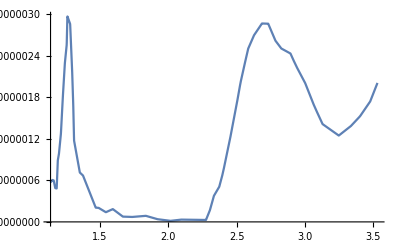

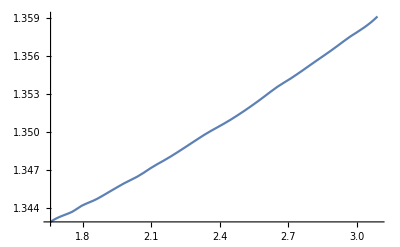

```mathematica
Plot[parteImPlasma[x],{x,1.14,3.53}]
Plot[parteRePlasma[x],{x,1.66,3.09}]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalosPlasma={{1.2,1.3},{2.57,2.8},{2.8,2.9},{3.4,3.5}};
epsPlasma[x_]:=epsIm[parteRePlasma,parteImPlasma,x];
epsPlasmaRe[x_]:=epsRe[parteRePlasma,parteImPlasma,x];
ω0iPlasma=ω0i[epsPlasma,intervalosPlasma];
```

InterpolatingFunction::dmval: Input value {1.2382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.2618} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.50004} lies outside the range of data in the interpolating function. Extrapolation will be used.

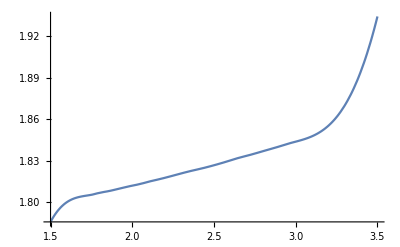

```mathematica
Plot[epsPlasmaRe[x],{x,1.5,3.5},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {1.13472} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.14472} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.15472} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

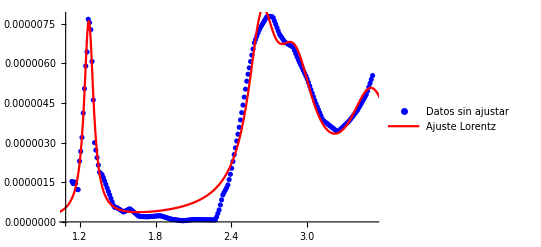

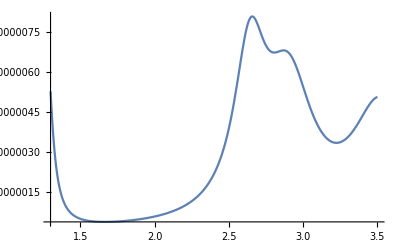

```mathematica
(*Ajuste de la parte imaginaria con lorentzianas*)
{xminPlasma,xmaxPlasma}={Min[datos2imPlasma],Max[datos2imPlasma]};
(*Datos para ajuste*)
epsPlasmaData=Table[{x,epsPlasma[x]},{x,xminPlasma,xmaxPlasma,0.01}];
(* Ajustar con NonlinearModelFit*)
fitPlasma=NonlinearModelFit[epsPlasmaData,lorentzSumIm4[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4],{{A1,0.01},{ω01,ω0iPlasma[[1]]},{γ1,0.05},{A2,0.01},{ω02,ω0iPlasma[[2]]},{γ2,0.05},{A3,0.01},{ω03,ω0iPlasma[[3]]},{γ3,0.05},{A4,0.01},{ω04,ω0iPlasma[[4]]},{γ4,0.05}},ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[epsPlasmaData,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fitPlasma[ω],{ω,xminPlasma-0.5,xmaxPlasma+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fitPlasma[ω],{ω,1.3,3.5},PlotRange->All]
```

```mathematica
ScientificForm[fitPlasma["BestFitParameters"],3]
```

{A1→8.66×10^-7,ω01→1.27,γ1→9.15×10^-2,A2→4.08×10^-6,ω02→2.65,γ2→2.61×10^-1,A3→5.69×10^-6,ω03→2.91,γ3→3.93×10^-1,A4→7.36×10^-6,ω04→3.53,γ4→4.66×10^-1}

```mathematica
parteIm0Plasma=Table[fitPlasma[x],{x,1.66,3.08,0.01}];
parteIm0Plasma10=Table[fitPlasma[x],{x,0,10,0.01}];
omegapruebaPlasma=Range[1.66,3.08,0.01];
datosRealObjetivoPlasma=epsPlasmaRe/@omegapruebaPlasma;
funcionErrorPlasma[w_?NumericQ]:=Module[{epsAnchor,espectro,dif},(*valor de epsReal en el ancla*)
epsAnchor=epsPlasmaRe[w];
(*ejecutar modelo*)espectro=sskkrebook[omegapruebaPlasma,parteIm0Plasma,w,epsAnchor];
(*error cuadrático total*)dif=espectro-datosRealObjetivoPlasma;
Sqrt[Total[dif^2]/Length[datosRealObjetivoPlasma]]];
```

```mathematica
holaPlasma=Table[{w,funcionErrorPlasma[w]},{w,1.66,3.08,0.01}];
```

Set::setraw: Cannot assign to raw object {1.66,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,«133»}.

Set::setraw: Cannot assign to raw object 3.68733×10^-7.

Set::setraw: Cannot assign to raw object 3.68701×10^-7.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
MinimalBy[holaPlasma,Last]
```

{{2.39,0.0126742}}

```mathematica
parteReSSKKPlasma=sskkrebook[omega10,parteIm0Plasma10,2.39,epsPlasmaRe[2.39]];
parterePlasma2=Interpolation[Transpose[{omega10,parteReSSKKPlasma}]];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.05547×10^-9.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

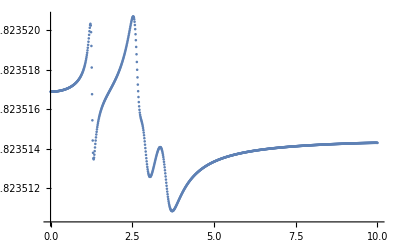

```mathematica
ListPlot[Transpose[{omega10,parteReSSKKPlasma}]]
```

```mathematica
h c/400
h c/1.5
```

3.10175

827.134

InterpolatingFunction::dmval: Input value {1.50003} lies outside the range of data in the interpolating function. Extrapolation will be used.

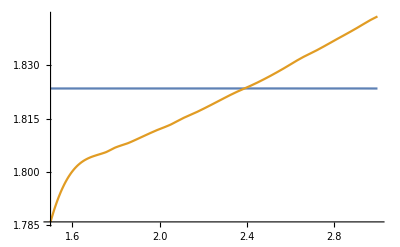

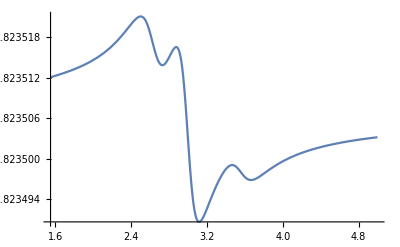

```mathematica
Plot[{parterePlasma2[x],epsPlasmaRe[x]},{x,1.5,3}]
Plot[{parterePlasma2[x]},{x,1.55,5}]
```

```mathematica
parteimPlasma=Interpolation[Transpose[{omega10,parteIm0Plasma10}]]
```

InterpolatingFunction[…]

```mathematica
epsPlasmaDataPHz=Table[{w*0.2418,parterePlasma2[w],parteimPlasma[w]},{w,1,10,0.01}];
Export["epsPlasmaDataPHz.csv",epsPlasmaDataPHz]
```

```mathematica
epsPlasmaDataPHz=Table[{(h c/l)*0.2418,parterePlasma2[h c/l],parteimPlasma[h c/l]},{l,400,800,50}];
Export["epsPlasmaDataPHz.csv",epsPlasmaDataPHz]
```

```mathematica
(h c/800)*0.2418
```

0.375002

```mathematica
1*0.2418
```

0.2418

```mathematica
parterePlasma2[1]
```

1.82352

```mathematica
parterePlasma2[w]
```

```mathematica
parterePlasma2[h c/850]
```

1.82352

```mathematica
8
```

## Plasma 2

```mathematica
(*Se van a importar los datos de la parte real del índice de refracción y del coeficiente de absorción*)
datosuAPlasma=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\uA_ImN_Plasma2.csv"];
datosRePlasma=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\ReN_Plasma.csv"];
(*Se eliminan los encabezados de los datos*)
datos1uAPlasma=Drop[datosuAPlasma,1];
datos1RePlasma=Drop[datosRePlasma,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2imPlasma=h c/datos1uAPlasma[[All,1]];
datos2rePlasma=h c/datos1RePlasma[[All,1]];
(*Obtener la parte imaginariad del índice de refracción a partir del coeficiente de absorción*)
datos3imPlasma=datos1uAPlasma[[All,2]]*10^(-6)*datos1uAPlasma[[All,1]]/(4*Pi);
(*Se interpolan los datos de la parte imaginaria*)
parteImPlasma=Interpolation[Transpose[{datos2imPlasma,datos3imPlasma}],InterpolationOrder->1];
parteRePlasma=Interpolation[Transpose[{datos2rePlasma,datos1RePlasma[[All,2]]}]];
```

InterpolatingFunction::dmval: Input value {1.14005} lies outside the range of data in the interpolating function. Extrapolation will be used.

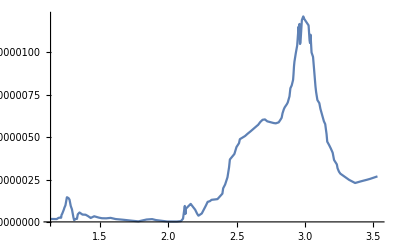

-Graphics-

```mathematica
Plot[parteImPlasma[x],{x,1.14,3.53}]
Plot[parteRePlasma[x],{x,1.66,3.09}]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalosPlasma={{1.2,1.3},{2.57,2.8},{2.8,2.9},{3.4,3.5}};
epsPlasma[x_]:=epsIm[parteRePlasma,parteImPlasma,x];
epsPlasmaRe[x_]:=epsRe[parteRePlasma,parteImPlasma,x];
ω0iPlasma=ω0i[epsPlasma,intervalosPlasma];
```

InterpolatingFunction::dmval: Input value {1.2382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.2618} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Plot[epsPlasmaRe[x],{x,1.5,3.5},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {1.50004} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

InterpolatingFunction::dmval: Input value {1.18496} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.19496} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.20496} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

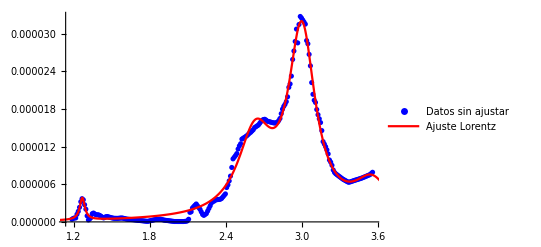

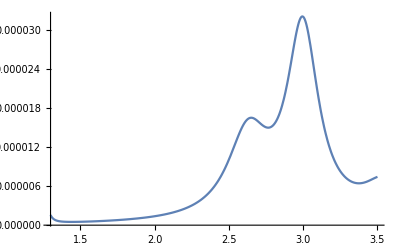

```mathematica
(*Ajuste de la parte imaginaria con lorentzianas*)
{xminPlasma,xmaxPlasma}={Min[datos2imPlasma],Max[datos2imPlasma]};
(*Datos para ajuste*)
epsPlasmaData=Table[{x,epsPlasma[x]},{x,xminPlasma,xmaxPlasma,0.01}];
(* Ajustar con NonlinearModelFit*)
fitPlasma=NonlinearModelFit[epsPlasmaData,lorentzSumIm4[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4],{{A1,0.01},{ω01,ω0iPlasma[[1]]},{γ1,0.05},{A2,0.01},{ω02,ω0iPlasma[[2]]},{γ2,0.05},{A3,0.01},{ω03,ω0iPlasma[[3]]},{γ3,0.05},{A4,0.01},{ω04,ω0iPlasma[[4]]},{γ4,0.05}},ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[epsPlasmaData,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fitPlasma[ω],{ω,xminPlasma-0.5,xmaxPlasma+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fitPlasma[ω],{ω,1.3,3.5},PlotRange->All]
```

```mathematica
ScientificForm[fitPlasma["BestFitParameters"],3]
```

{A1→8.66×10^-7,ω01→1.27,γ1→9.15×10^-2,A2→4.08×10^-6,ω02→2.65,γ2→2.61×10^-1,A3→5.69×10^-6,ω03→2.91,γ3→3.93×10^-1,A4→7.36×10^-6,ω04→3.53,γ4→4.66×10^-1}

```mathematica
parteIm0Plasma=Table[fitPlasma[x],{x,1.66,3.08,0.01}];
parteIm0Plasma10=Table[fitPlasma[x],{x,0,10,0.01}];
omegapruebaPlasma=Range[1.66,3.08,0.01];
datosRealObjetivoPlasma=epsPlasmaRe/@omegapruebaPlasma;
funcionErrorPlasma[w_?NumericQ]:=Module[{epsAnchor,espectro,dif},(*valor de epsReal en el ancla*)
epsAnchor=epsPlasmaRe[w];
(*ejecutar modelo*)espectro=sskkrebook[omegapruebaPlasma,parteIm0Plasma,w,epsAnchor];
(*error cuadrático total*)dif=espectro-datosRealObjetivoPlasma;
Sqrt[Total[dif^2]/Length[datosRealObjetivoPlasma]]];
```

```mathematica
holaPlasma=Table[{w,funcionErrorPlasma[w]},{w,1.66,3.08,0.01}];
```

Set::setraw: Cannot assign to raw object {1.66,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,«133»}.

Set::setraw: Cannot assign to raw object 6.55636×10^-7.

Set::setraw: Cannot assign to raw object 6.67357×10^-7.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
MinimalBy[holaPlasma,Last]
```

{{2.39,0.0126762}}

```mathematica
parteReSSKKPlasma=sskkrebook[omega10,parteIm0Plasma10,2.39,epsPlasmaRe[2.39]];
parterePlasma2=Interpolation[Transpose[{omega10,parteReSSKKPlasma}]];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.70221×10^-9.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

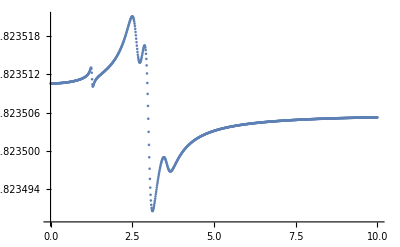

```mathematica
ListPlot[Transpose[{omega10,parteReSSKKPlasma}]]
```

```mathematica
h c/400
h c/800
```

3.10175

1.55088

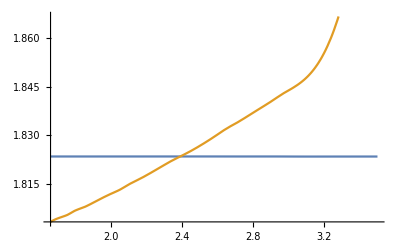

-Graphics-

```mathematica
Plot[{parterePlasma2[x],epsPlasmaRe[x]},{x,1.66,3.5}]
Plot[{parterePlasma2[x]},{x,1.55,5}]
```

```mathematica
parteimPlasma=Interpolation[Transpose[{omega10,parteIm0Plasma10}]]
```

InterpolatingFunction[…]

## Review Data

```mathematica
datosReview0=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\review_N_reported_KK.csv"];
datosReview1=Drop[datosReview0,1];
datosReview=Interpolation[Transpose[{datosReview1[[All,1]],datosReview1[[All,2]]}],InterpolationOrder->1];
datosFriebel0=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\review_N_reported_Friebel.csv"];
datosFriebel1=Drop[datosFriebel0,1];
datosFriebel=Interpolation[Transpose[{datosFriebel1[[All,1]],datosFriebel1[[All,2]]}],InterpolationOrder->1];
```

```mathematica
listReview=Table[{l,datosReview[l]},{l,400,700}];
listFriebel=Table[{l,datosFriebel[l]},{l,400,700}];
```

```mathematica
Mean[Abs[listReview[[All,2]]-listFriebel[[All,2]]]]
```

0.0194814

```mathematica
datosuAReview=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\review_uA_reported_KK.csv"];
datos1uAReview=Drop[datosuAPlasma,1];
datos2imReview=datos1uAReview[[All,1]];
datos3imReview=datos1uAReview[[All,2]]*10^(-6)*datos1uAReview[[All,1]]/(4*Pi);
(*Se interpolan los datos de la parte imaginaria*)
parteImReview=Interpolation[Transpose[{datos2imReview,datos3imReview}],InterpolationOrder->1];
```

InterpolatingFunction::dmval: Input value {256} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {260} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {264} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

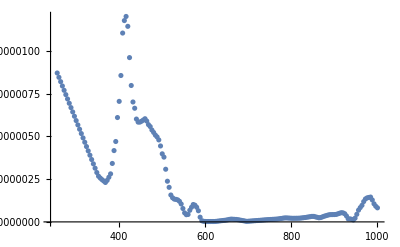

InterpolatingFunction::dmval: Input value {256} lies outside the range of data in the interpolating function. Extrapolation will be used.

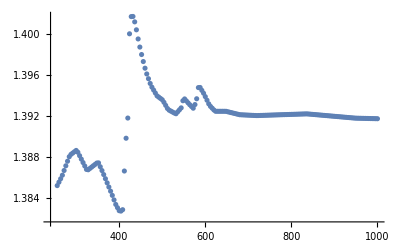

```mathematica
ListPlot[Table[{x,parteImReview[x]},{x,256,1000,4}],PlotRange->All]
ListPlot[Table[{x,datosReview[x]},{x,256,1000,4}],PlotRange->All]
```

```mathematica
epsReview[x_]:=epsRe[datosReview,parteImReview,x]
```

```mathematica
Plot[eps]
```

```mathematica
epsReview[550]
```

1.94219